# HW9

## Exercise 1

12.17 Since x is in the interior of S, there exists an open ball B(x, ϵ) that is a subset of S. There is a limit to the sequence {x_n}_(n = 1)^∞ (meaning there exists an N such that d(x_n, x) < ϵ for sufficiently large n).  Therefore, x_n ∈ B(x, ϵ). 

12.20 In a finite metric space S, all single points are closed (consider any {x_n}_(n = 1)^∞ in S that converges to x. x ∈ S).  The finite union of all single points in S is alsio closed.  The set of integers proof is the same as with the distance/metric function == 1. 

12.24 ?

12. 29
Let C be a closed subset of a compact set T.  U is an open cover of C.  Since C is closed, therefore T∖C is open in T.  if we add T∖C to U, we see that U∪(T∖C) is also an open cover of T.  As T is compact, there is a finite subcover of U, say V={U1,U2,…,Ur}.  This covers C by the fact that it covers T.  If T∖C is an element of V, then it can be removed from V and the rest of V still covers C.
Thus we have a finite subcover of U which covers C, and hence C is compact. (taken from Wikipedia)

## Exercise 2

Assume that there is a R-maximal element x^+ in the set S.
∀_x∈ S ¬ (x R x^+)

The strict lower contour set of the relationship on S is:
P_s = {y ∈ S | s P y} (where P is the asymmetric subrelation of R)

Since P_s is a cover of S
S ⊆ ∪_(a ∈ A)P_s_a

But by the strict lower contour set y ∈ S iff s P y.  Thus S ⊆ ∪_(a ∈ A)P_s_a.  We have a contradiction, so it must be the case that there exists no maximal element.

It is not the case that there is no R-maximal element in the set S iff the lower contour sets of the points x ∈ S form a cover of S because in this case the maximal element can be in the contour set.  Thus, there is no contradiction when the comntour set covers S.

## Exercise 3

Theorem:
Suppose that on a set X, an acyclic binary relation P has open lower contour sets. Then there exists a P-maximal element in any non-empty compact subset S ⊂ X.

Proof:
If there is no P-maximal element in S then every element in S is dominated by some other element in S:
∀_(s ∈ S) ∃_(s' ∈ S) s’ < s

The lower contour sets form a cover of S
S ⊆ ∪_(x ∈ S) (-∞ ... x)

The lower contour sets are open. Thus the lower contour sets are an open cover of S.

S is compact.  Thus, there is a finite subcover of S.  For each set in the subcover, pick any point in S for which it is the lower contour set.  The collection of such points is a finite set, A, of points whose lower contour sets cover S: 
S ⊆∪_(x∈A)(−∞ .. x).

 A is also covered by this ﬁnite subcover of S. So each point in A is “dominated” by some point in A. Since A is a ﬁnite set, which is only possible if P cycles.
 
 Definitions:
 A P-Maximal element is an element x^M such that ∀_(x ∈ X) (x^M P x) ∨ ¬(x P x^M)
 A cover C of a set S is a collection of sets such that S ⊆ ∪_(x ∈ A) C_x.  That is, some arbitrary union of the C_x contains S.
 A finite subcover is a subset of C that covers S under finite union.
 A set is compact iff there exists a finite subcover for any open subcover.
 The strict lower contour set is the P ⊆ X such that: P = ∃_(s ∈ X) {y ∈ S | s P y}.  That is every element on the lower contour set is strictly dominated by some element in the original set.
 An open set S ∈ τ of the topology (X, τ) which is defined by:
 x, ∅ ∈ τ
V_1, V_2 ∈ τ ⇒ V_1 ∩ V_2 ∈ τ
 (∀_(α ∈ I) V_α ∈ τ) ⇒ ∪_(α ∈ I)V_α ∈ τ.

## Exercise 4

Consider a point q ∈ K.  Then by Hausdorf condition, there exists open neighborhoods N(q) and N(p) such that N(q) ∩ N(p) = ∅. K ⊆ ∪_(q ∈ K) N(q).  That is N(q) is an open subcover of N(q).  Since K is compact set, there is a finite subcover of K.n Let U be the union of the finite subcover of A.  For eah set in the finite subcover there is a collection of open neighborhoods of p.  Let U be the intersection of all these neighborhoods.  Then V is an open set containing K that does not intersect U.

## Exercise 5

A metric space is a set for which, for any pair of elements in the set, a distance function is defined.  The distance function must follow these properties:
d(x, y) ≥ 0
d(x, y) = d (y, x)
d(x, y) = 0 ⇔ x = y
d(x, z) ≤ d(x, y) + d(y, z)

The function f(x, x’) given for this problem satisfies these properties.  f(x, x’) can only take on the values 0 and 1 and is equal to 0 if x = x’ and 1 otherwise.   It is the case that if x = x’ then d(x, x’) = d(x’ x) = 0.  Otherwise d(x, x’) = 1.  Finally if y, z = x then d(x, y) = 0, d(y, z) = 0 ≤ d(x, z) = 0.  Otherwise if x ≠ y then d(x, z) = ≤ d(x, y) + d(y, z)  ⟶ 1 ≤ 0 + 1 or if x ≠ z then d(x, z) = ≤ d(x, y) + d(y, z) ⟶ 1 ≤ 0 + 1 or x ≠ y ≠ z then d(x, z) ≤ d(x,y) + d(x,z) ⟶ 1 ≤ 2.

## Exercise 6

Case 1: Assume z > x and y > z
|1/x - 1/z| ≤ |1/x - 1/y| + |1/y - 1/z|
We rearrange the above using assumptions so it is strictly positive
1/x - 1/z ≤ 1/x - 1/y + 1/z - 1/y
1/x - 1/x - 1/z - 1/z ≤ -2/y
-2/z ≤ -2/y
-2y ≤ -2z
y ≥ z

x = 1, y = 3, z = 2
|1/1 - 1/2| ≤ |1/1 - 1/3| + |1/3 - 1/2|
1/2 ≤ 2/3 + 1/6

Case 2: Assume z > x and z > y
|1/x - 1/z| ≤ |1/x - 1/y| + |1/3 - 1/2|
We drop the absolute value signs because the differencses above are all strictly positive given the assumptions
1/x - 1/z ≤ 1/x - 1/y + 1/y - 1/z
which simplifies to
1/x - 1/z ≤ 1/x - 1/z which is true

Case 3: Assume z > x and x > y
|1/x - 1/z| ≤ |1/x - 1/y| + |1/3 - 1/2|
We rearrange the above using assumptions so it is strictly positive
1/x - 1/z ≤ 1/y - 1/x + 1/z - 1/y
which simplifies to
1/x - 1/z ≤ 1/z - 1/x
2/x ≤ 2/z
2z ≤ 2x
z ≤ x which is true.

The other cases are trivially true:
|x| ≥ 0 by definition of |x|
|1/x - 1/x| = 0
|1/x-1/y|=|1/y-1/x| by symmetry property of |x - y| (that is |x - y| = |y - x|

## Exercise 7

Let S be a compact set and let x ∈ S.  The set S is bounded, if ∀_(s ∈ S) d(x, s) < M where M is a positive integer.

Let B(x, r) = {y ∈ S| d(x, y) < r} be an open ball with center x and radius r.

For any y ∈ S, y ∈ ∪_(i = 1)^∞B(x, i) since d(x, y) < ∞.  Therefore {B(x, i)} is an open cover of S.  Since S is compact, there is a finite subcover such that:
S ⊂ ∪_(j=1)^m B(x, i_j).
This means S ⊂ B(x, max{i_1, ... i_j}). Therefore S is bounded.

## Exercise 8

Suppose (x_t_k) is subsequence of (x_t) that converges to x̄.  There exists a positive real number such that:
∀_(i,j∈ℕ) i, j > M⟹d (x_i, x_j)< ϵ/2.  By definition of convergence ∀k∈N k > N⟹d(xnk,x) < e/2.  By the triangle inequality, we have 
∀_(m ∈ ℕ) m > K ⟹ d(x_m,x) ≤ d(x_m,x) + d(x_nK,x) < ϵ/2 + ϵ/2 = ϵ

## Comnputation 1

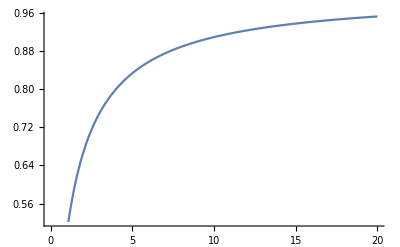

```mathematica
Plot[t/(t+1),{t,0,20}]
```

A series is monotone if ∀_(m>n) s_m > s_n (monotone increasing) or  ∀_(m>n) s_m < s_n (monotone decreasing).  A sequence is bounded if ∃_(x ∈ R) s_n < x.  A sequence is convergent if there exists a N ∈ ℕ such that  for any n > N, |x_n - x | < ϵ.
My seuqnce is monotone bounded and convergent.

```mathematica
Limit[t/t+1, t -> ∞]
```

2

## Computational Exercise 2

```mathematica
pdv[savings_, rate_] := (
dv={};
Do[AppendTo[dv,(savings[[i]]/(1+ rate)^(i-1))],{i, 1, Length[savings]}];
Return [Total[dv]])
```

```mathematica
pdv[Table[200,60], .01]
Print[StringForm["The Present value of 60 payments of 200 at a 1% monthly interest rate is ``",Round[%, 2]]]
```

9080.92

The Present value of 60 payments of 200 at a 1% monthly interest rate is 9080